## Probability of single resistance for the EG model with constant birth and death rates

## Input

```mathematica
ClearAll["Global`*"]
```

```mathematica
<<MaTeX`
```

```mathematica
bS=1.0;
bA=1.1;
bB=1.2;
bD=1.3;
dS=0.1 ;
dA=0.1;
dB=0.1;
dD=0.1;
μA= 1 10^-4;
μB= 1 10^-4;
rS = bS(1-μA-μB)-dS;
rA = bA(1 - μB) - dA;
rB = bB(1 - μA) - dB;
rD = bD - dD;
n0 = 10^4;
```

## Single resistance

### Analytics

```mathematica
PhiASingle[bS_, bA_, bB_, bD_, dS_, dA_, dB_, dD_,μA_,μB_,n0_, T_]:=-n0 bS μA (bA(1 - μB) - dA)(1/(bA ( bS(1-μA-μB)-dS)(1-μB))(ⅇ^((bS(1-μA-μB)-dS) T) Hypergeometric2F1[1,(bS(1-μA-μB)-dS)/(bA(1 - μB) - dA),(bA(1 - μB) - dA+bS(1-μA-μB)-dS)/(bA(1 - μB) - dA),dA/(bA(1- μB))]-Hypergeometric2F1[1,(bS(1-μA-μB)-dS)/(bA(1 - μB) - dA),(bA(1 - μB) - dA+bS(1-μA-μB)-dS)/(bA(1 - μB) - dA),(dA ⅇ^(-(bA(1 - μB) - dA)T))/(bA(1-μB))])); 
PhiBSingle[bS_, bA_, bB_, bD_, dS_, dA_, dB_, dD_,μA_,μB_,n0_, T_]:=-n0 bS μB (bB(1 - μA) - dB)(1/(bB ( bS(1-μB-μA)-dS)(1-μA))(ⅇ^((bS(1-μA-μB)-dS) T) Hypergeometric2F1[1,(bS(1-μA-μB)-dS)/(bB(1 - μA) - dB),(bB(1 - μA) - dB+bS(1-μA-μB)-dS)/(bB(1 - μA) - dB),dB/(bB(1- μA))]-Hypergeometric2F1[1,(bS(1-μA-μB)-dS)/(bB(1 - μA) - dB),(bB(1 - μA) - dB+bS(1-μA-μB)-dS)/(bB(1 - μA) - dB),(dB ⅇ^(-(bB(1 - μA) - dB)T))/(bB(1- μA))]));
PRSingle[bS_, bA_, bB_, bD_, dS_, dA_, dB_, dD_,μA_,μB_,n0_, T_]:=1-Exp[PhiASingle[bS, bA, bB, bD, dS, dA, dB, dD,μA,μB,n0, T]+PhiBSingle[bS, bA, bB, bD, dS, dA, dB, dD,μA,μB,n0, T]];
```

### 2D Plot

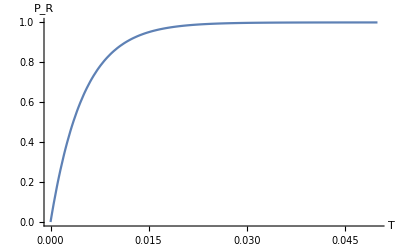

```mathematica
Plot[PRSingle[bS, bA, bB, bD, dS, dA, dB, dD,μA,μB,10^6, T],{T,0,0.05},PlotRange->All,AxesLabel->{"T","P_R"}]
```

### Contour Plot

#### Table plot (general)

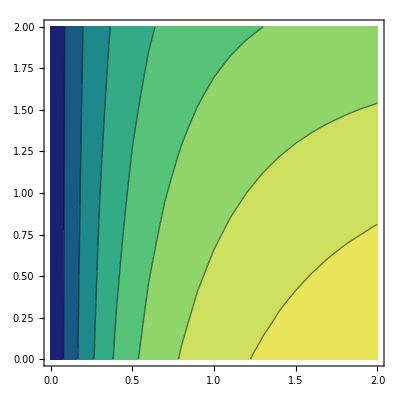

```mathematica
minT=0;maxT = 2;  dT = 0.1; minp=0;maxp =2;dp = 0.1;
pstring="dS";
dat=Table[PRSingle[bS, bA, bB, bD, dS, dA, dB, dD,μA,μB,n0, T],{dS,minp,maxp,dp},{T,minT,maxT,dT}] ;plot=ListContourPlot[dat,PlotRange->All,Contours->Append[Table[k,{k,0,0.99,0.15}],0.99],ColorFunctionScaling->False,ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[{"BlueGreenYellow",{0,1}},LabelStyle->{FontColor->"Black",FontSize->21,FontFamily->"Latin Modern Roman"},LegendLabel->MaTeX["P_{R}^{\\text{single}}",Magnification->2.5]],{After,Top}],FrameLabel->{MaTeX["T",Magnification->2.5],If[StringLength[pstring]==2,MaTeX[StringInsert[pstring,"_",2],Magnification->2.5],MaTeX[StringJoin["\\",StringInsert[pstring,"_",3]],Magnification->2.5]]},PlotRange->All,DataRange->{{minT,maxT},{minp,maxp}}, BaseStyle->{FontColor->"Black",FontFamily -> "Latin Modern Roman",FontSize->22},Frame->True]
```

#### Table plot (varying n0)

```mathematica
minT=0;maxT = 2;  dT = 0.1; minp=0;maxp =10000;dp = 100;
pstring="n0";
dat=Table[PRSingle[bS, bA, bB, bD, dS, dA, dB, dD,μA,μB,n0, T],{n0,minp,maxp,dp},{T,minT,maxT,dT}] ;
```

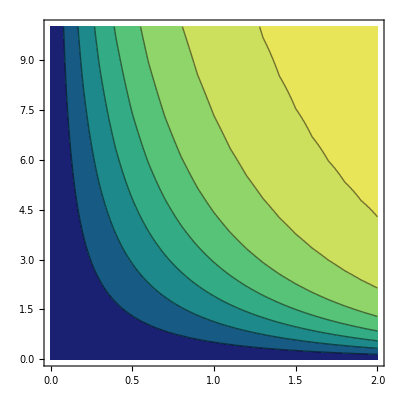

```mathematica
plot=ListContourPlot[ToExpression[dat],PlotRange->All,Contours->Append[Table[k,{k,0,0.99,0.15}],0.99],ColorFunction->"BlueGreenYellow",ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{"BlueGreenYellow",{0,1}},LabelStyle->{FontColor->"Black",FontSize->21,FontFamily->"Latin Modern Roman"},LegendLabel->MaTeX["P_{R}^{\\text{single}}",Magnification->2.0]],{After,Top}],FrameLabel->{MaTeX["T",Magnification->2.5],MaTeX["n_0 (\\times 10^3)",Magnification->2.5]},PlotRange->All,DataRange->{{0,maxT},{0,10}}, BaseStyle->{FontColor->"Black",FontFamily -> "Latin Modern Roman",FontSize->22},Frame->True]
```

#### Table plot (varying μ)

```mathematica
minT=0;maxT = 2;  dT = 0.05; minp=0;maxp =10^-4;dp = 10^-5;
pstring = "muA";
dat=Table[PRSingle[bS, bA, bB, bD, dS, dA, dB, dD,μA,μB,n0, T],{μA,minp,maxp,dp},{T,minT,maxT,dT}] ;
```

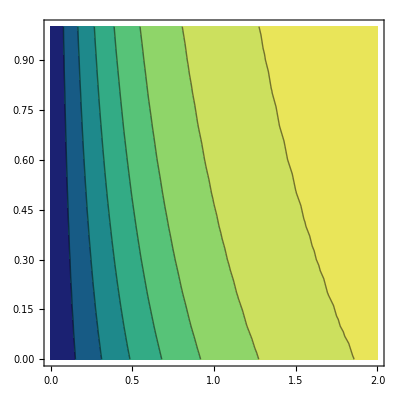

```mathematica
plot=ListContourPlot[dat,PlotRange->All,Contours->Append[Table[k,{k,0,0.99,0.15}],0.99],ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[{"BlueGreenYellow",{0,1}},LabelStyle->{FontColor->"Black",FontSize->21,FontFamily->"Latin Modern Roman"},LegendLabel->MaTeX["P_{R}^{\\text{single}}",Magnification->2.0]],{After,Top}],FrameLabel->{MaTeX["T",Magnification->2.5],MaTeX["\\mu_A (\\times 10^{-4})",Magnification->2.5]},PlotRange->All,DataRange->{{0,maxT},{0,1}}, BaseStyle->{FontColor->"Black",FontFamily -> "Latin Modern Roman",FontSize->22},Frame->True]
```

### Export data

```mathematica
SetDirectory[NotebookDirectory[]];
folder = "linear-param-1-";
Export[FileNameJoin[{Directory[],"parameters-1/1.linear-model",StringJoin[folder,pstring,"-PRS-v3.pdf"]}],plot]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Export[FileNameJoin[{Directory[],"parameters-1/1.linear-model",StringJoin[folder,pstring,"-PRS.txt"]}],dat,"Table","FieldSeparators"->" "]
Export[FileNameJoin[{Directory[],"parameters-1/1.linear-model",StringJoin[folder,pstring,"-PRS-time.txt"]}],Table[T,{T,0,maxT, dT}],"Table","FieldSeparators"->" "]
Export[FileNameJoin[{Directory[],"parameters-1/1.linear-model",StringJoin[folder,pstring,"-PRS-parameter.txt"]}],Table[p,{p,minp,maxp, dp}],"Table","FieldSeparators"->" "]
```

## Double resistance

### Analytics

```mathematica
PhiADouble[bS_, bA_, bB_, bD_, dS_, dA_, dB_, dD_,μA_,μB_,n0_, T_]:=n0 bA μB (bD - dD)((bS μA)/(bS(1-μA-μB)-dS - (bA(1 - μB) - dA)))(1/(bD (bA(1 - μB) - dA))(ⅇ^((bA(1 - μB) - dA)T) Hypergeometric2F1[1,(bA(1 - μB) - dA)/(bD - dD),(bA(1 - μB) - dA+bD - dD)/(bD - dD),dD/bD]-Hypergeometric2F1[1,(bA(1 - μB) - dA)/(bD - dD),(bA(1 - μB) - dA+bD - dD)/(bD - dD),(dD ⅇ^(-(bD - dD)T))/bD])); 
PhiBDouble[bS_, bA_, bB_, bD_, dS_, dA_, dB_, dD_,μA_,μB_,n0_, T_]:=n0 bB μA (bD - dD)((bS μB)/(bS(1-μA-μB)-dS - (bB(1 - μA) - dB)))(1/(bD (bB(1 - μA) - dB))(ⅇ^((bB(1 - μA) - dB) T) Hypergeometric2F1[1,(bB(1 - μA) - dB)/(bD - dD),(bB(1 - μA) - dB+bD - dD)/(bD - dD),dD/bD]-Hypergeometric2F1[1,(bB(1 - μA) - dB)/(bD - dD),(bB(1 - μA) - dB+bD - dD)/(bD - dD),(dD ⅇ^(-(bD - dD) T))/bD]));
PhiSDouble[bS_, bA_, bB_, bD_, dS_, dA_, dB_, dD_,μA_,μB_,n0_, T_]:=-n0 (bD - dD) (bA μB ((bS μA)/(bS(1-μA-μB)-dS - (bA(1 - μB) - dA))) + bB μA ((bS μB)/(bS(1-μA-μB)-dS - (bB(1 - μA) - dB))))(1/(bD ( bS(1-μA-μB)-dS))(ⅇ^(( bS(1-μA-μB)-dS) T) Hypergeometric2F1[1,(bS(1-μA-μB)-dS)/(bD - dD),(bD - dD+ bS(1-μA-μB)-dS)/(bD - dD),dD/bD]-Hypergeometric2F1[1,(bS(1-μA-μB)-dS)/(bD - dD),(bD - dD+ bS(1-μA-μB)-dS)/(bD - dD),(dD ⅇ^(-(bD - dD)T))/bD]));
PRDouble[bS_, bA_, bB_, bD_, dS_, dA_, dB_, dD_,μA_,μB_,n0_, T_]:=1-Exp[PhiADouble[bS, bA, bB, bD, dS, dA, dB, dD,μA,μB,n0, T]+PhiBDouble[bS, bA, bB, bD, dS, dA, dB, dD,μA,μB,n0, T] + PhiSDouble[bS, bA, bB, bD, dS, dA, dB, dD,μA,μB,n0, T]];
```

### 2D Plot

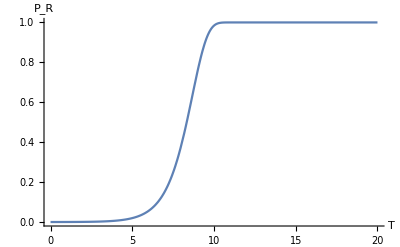

```mathematica
Plot[PRDouble[bS, bA, bB, bD, 2, dA, dB, dD,μA,μB,n0, T],{T,0,20},PlotRange->All,AxesLabel->{"T","P_R"}]
```

### Contour Plot

#### Table plot (general)

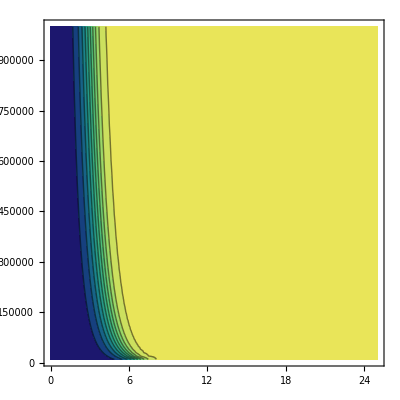

```mathematica
minT=0;dT = 0.125; maxT = 25; 
minp=10^4;dp = 10^4; maxp =10^6;
pstring="n0";
dat=Table[PRDouble[bS, bA, bB, bD, dS, dA, dB, dD,μA,μB,n0, T],{n0,minp,maxp,dp},{T,0,maxT,dT}];plot=ListContourPlot[dat,PlotRange->All,Contours->Append[Table[k,{k,0,0.99,0.1}],0.99],ColorFunction->"BlueGreenYellow",ColorFunctionScaling->False,PlotLegends->Placed[BarLegend[{"BlueGreenYellow",{0,1}},LabelStyle->{FontColor->"Black",FontSize->21,FontFamily->"Latin Modern Roman"},LegendLabel->MaTeX["P_{R}^{\\text{double}}",Magnification->2.0]],{After,Top}],FrameLabel->{MaTeX["T",Magnification->2.5],If[StringLength[pstring]==2,MaTeX[StringInsert[pstring,"_",2],Magnification->2.5],MaTeX[StringJoin["\\",StringInsert[pstring,"_",3]],Magnification->2.5]]},PlotRange->All,DataRange->{{minT,maxT},{minp,maxp}}, BaseStyle->{FontColor->"Black",FontFamily -> "Latin Modern Roman",FontSize->22},Frame->True]
```

#### Table plot (varying n0)

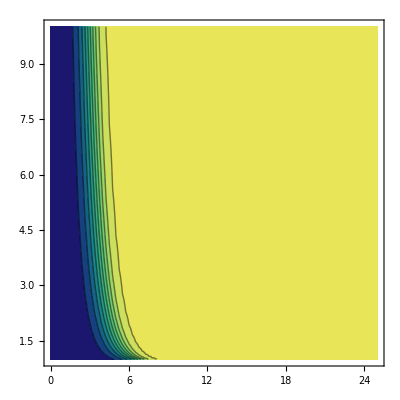

```mathematica
minT=0;dT = 0.25; maxT = 25; 
minp=10^4;dp = 5 10^3; maxp =10^6;
pstring="n0";
dat=Table[PRDouble[bS, bA, bB, bD, dS, dA, dB, dD,μA,μB,n0, T],{n0,minp,maxp,dp},{T,0,maxT,dT}];
plot=ListContourPlot[dat,PlotRange->All,Contours->Append[Table[k,{k,0,0.99,0.1}],0.99],ColorFunction->"BlueGreenYellow",PlotLegends->Placed[BarLegend[{"BlueGreenYellow",{0,1}},LabelStyle->{FontColor->"Black",FontSize->21,FontFamily->"Latin Modern Roman"},LegendLabel->MaTeX["P_{R}^{\\text{double}}",Magnification->2.0]],{After,Top}],FrameLabel->{MaTeX["T",Magnification->2.5],MaTeX["n_0 (\\times 10^5)",Magnification->2.5]},PlotRange->All,DataRange->{{minT,maxT},{1,10}}, BaseStyle->{FontColor->"Black",FontFamily -> "Latin Modern Roman",FontSize->22},Frame->True]
```

### Export data

```mathematica
SetDirectory[NotebookDirectory[]];
folder="";
filename = "linear-param-1-n0-PRD";
Export[FileNameJoin[{Directory[],folder,StringJoin[filename,".pdf"]}],plot]
```